```mathematica
SetDirectory["/Users/Apple/Documents/GitHub/LaTeX-Files/中级化学实验报告/data/Fluorescence"];
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Real}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

```mathematica
TableForm[Transpose[{Range[Length[#]],#}]&@FileNames["*.TXT"]]
```

1 | 0_5_2ND.TXT
2 | 0_5EM2ND.TXT
3 | 0_5EMIT'.TXT
4 | 0_5EMIT.TXT
5 | 0_5'.TXT
6 | 0_5.TXT
7 | 10MLACOH.TXT
8 | 20MLACOH.TXT
9 | 5MLACOH.TXT
10 | BACK'.TXT
11 | BACK.TXT
12 | PH_MIN'.TXT
13 | PH_MIN.TXT
14 | STANDARD.TXT
15 | UNKNOWN.TXT

```mathematica
A[14]
```

{}

```mathematica
Fit[{#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"),{1,x},x]
```

14.1588+2734.31 x

```mathematica
Solve[14.158799999999832+2734.3137499999993 x==272.407,x]
```

{{x→0.0944472}}

```mathematica
LinearModelFit[{#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"),{1,x},x]["RSquared"]
```

0.999613

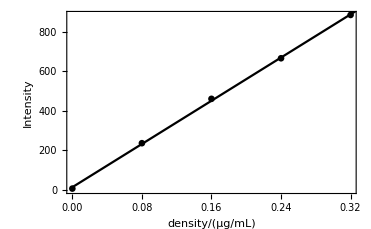

```mathematica
Show[
ListPlot[#,Axes->False,Frame->True,PlotStyle->Black,FrameLabel->{"density/(μg/mL)","Intensity"}],
Plot[14.158799999999832+2734.3137499999993 x,{x,0,1},PlotStyle->Black]
]&@({#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"))
```

```mathematica
Export["Standardcurve.eps",%]
```

Standardcurve.eps

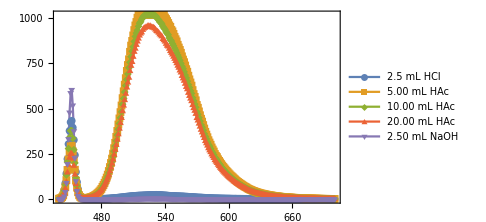

```mathematica
ListLinePlot[{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])},PlotRange->All,PlotMarkers->{Automatic,8},ImageSize->Medium,Frame->True,Axes->False,PlotLegends->{"2.5 mL HCl","5.00 mL HAc","10.00 mL HAc","20.00 mL HAc","2.50 mL NaOH"},ImageSize->Large]
```

```mathematica
Position[#,1]&/@(PeakDetect[#,0,2,200]&/@(#2&@@@Transpose/@{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])}))
```

{{{13}},{{13}},{{12},{83}},{{13},{85},{87}},{{13}}}

```mathematica
functionlist=Interpolation[#][x]&/@{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])};
```

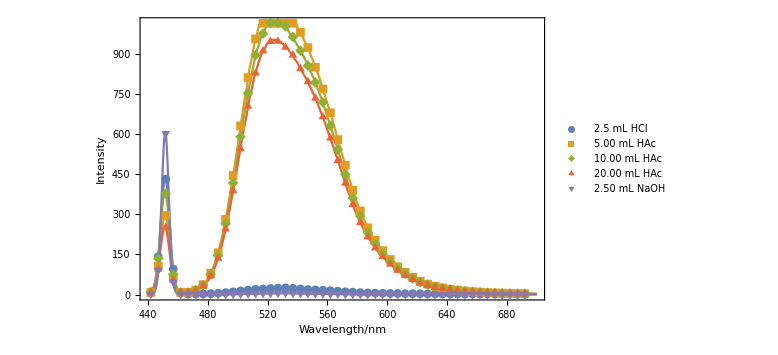

```mathematica
Show[Plot[functionlist,{x,440,700},PlotRange->All,ImageSize->Medium,Frame->True,Axes->False,ImageSize->Large,FrameLabel->{"Wavelength/nm","Intensity"}],ListPlot[Part[#,Table[5i+3,{i,0,50}]]&/@{A[13],A[9],A[7],A[8],({#1,50(#2/100)^1.7}&@@@A[13])},PlotMarkers->Automatic,PlotLegends->{"2.5 mL HCl","5.00 mL HAc","10.00 mL HAc","20.00 mL HAc","2.50 mL NaOH"},FrameTicks->True],ImageSize->Large]
```

```mathematica
Export["pH.eps",%]
```

pH.eps

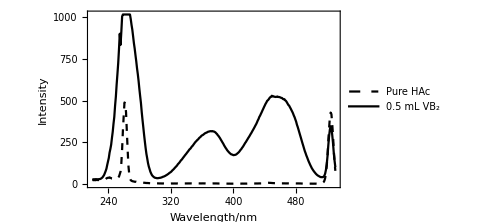

```mathematica
ListLinePlot[{A[11],A[6]},PlotRange->All,ImageSize->Medium,Frame->True,PlotStyle->{{Black,Dashed},{Black}},Axes->False,PlotLegends->{"Pure HAc","0.5 mL VB_2"},FrameLabel->{"Wavelength/nm","Intensity"}]
```

```mathematica
Export["expose.eps",%]
```

expose.eps

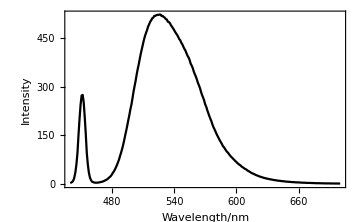

```mathematica
ListLinePlot[A[4],PlotRange->All,ImageSize->Medium,Frame->True,PlotStyle->Black,Axes->False,FrameLabel->{"Wavelength/nm","Intensity"}]
```

```mathematica
Export["emission.eps",%]
```

emission.eps

```mathematica
({#1/25*10,#2}&@@@(Drop[#,1]&/@Cases[Import[#,"Table"],{_Integer,_Real,_Real}]&@"STANDARD.TXT"))//Transpose//TableForm//TeXForm
```

\begin{array}{ccccc}
 0. & 0.08 & 0.16 & 0.24 & 0.32 \\
 7.154 & 236.915 & 461.473 & 666.732 & 885.971 \\
\end{array}

```mathematica
-Log10/@(ComplexH[{#/60.06,0},{1.8*10^(-5)}]&/@{1/5,10/25,20/25})
```

{3.6271,3.47191,3.31809}

```mathematica
-Log10@ComplexH[{0.6,0},{10000}]
```

0.221875

```mathematica
-Log10@ComplexH[{0,10/40/10},{0}]
```

12.3979

```mathematica
FindFit[Drop[A[4],84],a E^((x-μ)^2/(2 σ^2))(1-E^(k x))+b,{a,σ,μ,k,b},x]
```

Drop::drop: Cannot drop positions 1 through 84 in A[4].

FindFit::fitd: First argument Drop[A[4],84] in FindFit is not a list or a rectangular array.

FindFit[Drop[A[4],84],b+a ⅇ^((x-μ)^2/(2 σ^2)) (1-ⅇ^(k x)),{a,σ,μ,k,b},x]

```mathematica
Drop[A[4],84]
```

{{524.,521.506},{525.,521.359},{526.,522.496},{527.,522.154},{528.,517.867},{529.,518.268},{530.,514.76},{531.,513.079},{532.,508.722},{533.,507.168},{534.,500.293},{535.,499.224},{536.,495.835},{537.,489.656},{538.,484.948},{539.,479.998},{540.,474.977},{541.,469.252},{542.,464.138},{543.,459.471},{544.,453.627},{545.,446.725},{546.,443.147},{547.,435.361},{548.,430.658},{549.,423.093},{550.,416.429},{551.,411.197},{552.,402.821},{553.,395.363},{554.,390.293},{555.,382.309},{556.,371.174},{557.,365.144},{558.,357.615},{559.,347.074},{560.,338.575},{561.,331.374},{562.,322.162},{563.,311.74},{564.,304.197},{565.,295.519},{566.,284.246},{567.,274.28},{568.,266.709},{569.,257.575},{570.,245.764},{571.,238.457},{572.,227.775},{573.,218.688},{574.,209.528},{575.,201.332},{576.,193.621},{577.,183.56},{578.,175.382},{579.,168.841},{580.,161.659},{581.,154.175},{582.,147.856},{583.,141.713},{584.,135.154},{585.,129.838},{586.,124.108},{587.,117.701},{588.,113.928},{589.,109.168},{590.,103.951},{591.,99.762},{592.,96.715},{593.,92.215},{594.,87.976},{595.,84.321},{596.,81.402},{597.,77.9},{598.,74.636},{599.,71.168},{600.,68.56},{601.,65.215},{602.,62.175},{603.,59.926},{604.,57.72},{605.,54.532},{606.,52.338},{607.,50.386},{608.,47.718},{609.,46.331},{610.,44.091},{611.,41.602},{612.,39.882},{613.,37.974},{614.,35.741},{615.,33.68},{616.,32.852},{617.,31.119},{618.,29.594},{619.,27.907},{620.,26.799},{621.,25.519},{622.,24.069},{623.,23.228},{624.,22.033},{625.,21.163},{626.,20.007},{627.,19.107},{628.,18.465},{629.,17.338},{630.,17.06},{631.,16.015},{632.,15.418},{633.,14.942},{634.,14.12},{635.,13.688},{636.,13.028},{637.,12.355},{638.,12.21},{639.,11.354},{640.,11.175},{641.,10.622},{642.,10.34},{643.,9.806},{644.,9.318},{645.,9.138},{646.,8.864},{647.,8.282},{648.,8.055},{649.,7.689},{650.,7.524},{651.,7.28},{652.,7.125},{653.,6.515},{654.,6.476},{655.,6.306},{656.,6.044},{657.,5.769},{658.,5.559},{659.,5.503},{660.,5.517},{661.,5.251},{662.,5.074},{663.,4.642},{664.,4.604},{665.,4.555},{666.,4.413},{667.,4.252},{668.,3.956},{669.,3.955},{670.,3.945},{671.,3.932},{672.,3.69},{673.,3.522},{674.,3.588},{675.,3.321},{676.,3.232},{677.,2.99},{678.,2.977},{679.,3.192},{680.,2.904},{681.,2.891},{682.,2.852},{683.,2.696},{684.,2.625},{685.,2.564},{686.,2.408},{687.,2.478},{688.,2.421},{689.,2.508},{690.,2.329},{691.,2.276},{692.,2.192},{693.,2.273},{694.,2.211},{695.,2.073},{696.,2.133},{697.,2.128},{698.,2.025},{699.,2.018},{700.,2.023}}

```mathematica
-Log10/@(ComplexH[{#/60.06,0},{1.8*10^(-5)}]&/@{1/5,10/25,20/25})

-Log10@ComplexH[{0.6,0},{10000}]

-Log10@ComplexH[{0,10/40/10},{0}]
```

{3.6271,3.47191,3.31809}

0.221875

12.3979

```mathematica
25/0.4*0.0944
```

5.9

```mathematica
SetDirectory["F:\\GitHub\\Elucate\\中级化学实验报告\\data\\Chromatography"];
```

```mathematica
FileNames[]
```

{std-01.txt,std-02.txt,std-03.txt,std-04.txt,std-05.txt,std-06.txt,std-07.txt,std-08.txt,std-09.txt,std-10.txt,std-11.txt,std-12.txt}

```mathematica
Table[A[i]=Cases[Import[#[[i]],"Table"],{_Real,_Integer}],{i,1,Length[#]}]&@FileNames["*.TXT"];
```

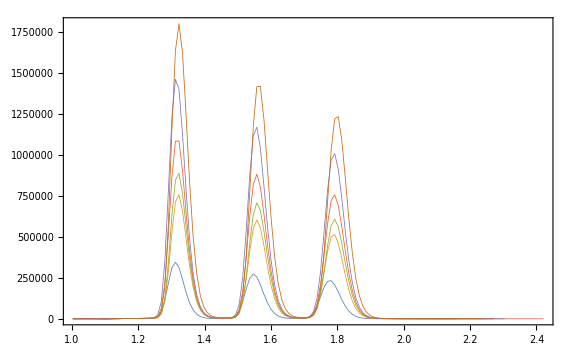

```mathematica
ListLinePlot[Select[#,#[[1]]>1&]&/@A/@Range[6],PlotRange->All,PlotStyle->Thickness[0.001],ImageSize->Large,Frame->True,Axes->False]
```

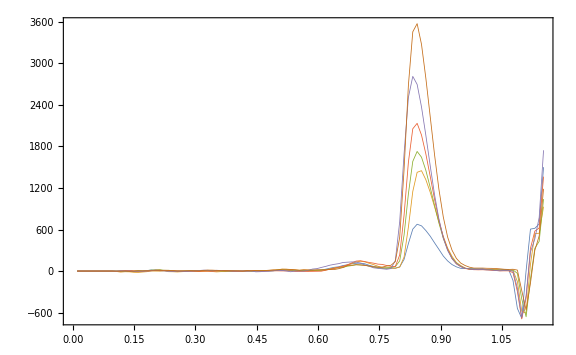

```mathematica
ListLinePlot[Select[#,0<#[[1]]<1.16&]&/@A/@Range[6],PlotRange->All,PlotStyle->Thickness[0.001],ImageSize->Large,Frame->True,Axes->False]
```

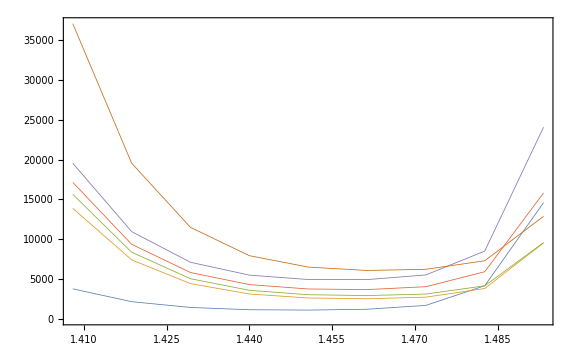

```mathematica
ListLinePlot[Select[#,1.4<#[[1]]<1.5&]&/@A/@Range[6],PlotStyle->Thickness[0.001],ImageSize->Large,Frame->True,Axes->False]
```